```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(*Load core activity, converting all date/times into DateObjects*)
```

```mathematica
coreActivity = Import["activity.tsv", "TSV"];coreActivity[[Range[2, Length[coreActivity]],3]]=(DateObject[StringDrop[#,-8]] &)/@coreActivity[[Range[2, Length[coreActivity]],3]];coreActivity[[Range[2, Length[coreActivity]],4]]=(DateObject[StringDrop[#,-8]] &)/@coreActivity[[Range[2, Length[coreActivity]],4]];
```

```mathematica
startTime=Sort[coreActivity[[Range[2, Length[coreActivity]],3]]][[1]]
```

Sun 29 Nov 2015 12:55:00

```mathematica
endTime=Reverse[Sort[coreActivity[[Range[2, Length[coreActivity]],4]]]][[1]]
```

Fri 4 Dec 2015 18:23:00

```mathematica
(*Exclude job flows that failed to start from prep activity*)
```

```mathematica
prepActivity=Select[coreActivity[[Range[2,Length[coreActivity]]]], #[[2]]=="prep" && #[[8]]==0&];
```

```mathematica
alignActivity=Select[coreActivity[[Range[2,Length[coreActivity]]]], #[[2]]=="align" && #[[8]]==0&];
```

```mathematica
prepPiece=Total[Piecewise[{{1, QuantityMagnitude[#[[3]]-startTime]≤x≤ QuantityMagnitude[#[[4]]-startTime]}}]&/@prepActivity] *80;
```

```mathematica
alignPiece=Total[Piecewise[{{1, QuantityMagnitude[#[[3]]-startTime]≤x≤ QuantityMagnitude[#[[4]]-startTime]}}]&/@alignActivity]*2560;
```

```mathematica
(*First plot is of number of active cores in time during preprocess job flows; second plot is of number of active cores in time during align job flows*)
```

```mathematica
interval=.01; dateRange=Range[0, QuantityMagnitude[endTime-startTime], interval];
```

```mathematica
imagePadding={{70,30},{50,30}};
```

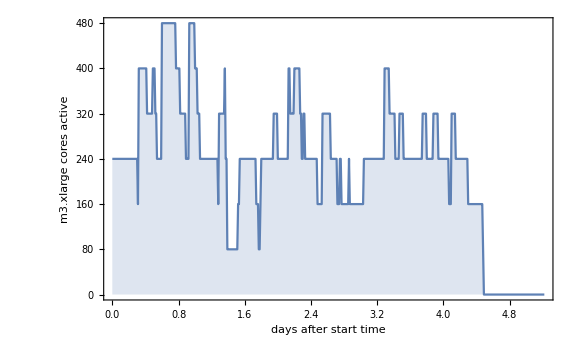

```mathematica
prepPlot=ListPlot[Transpose[{dateRange,(prepPiece/.x->#)&/@dateRange}], Joined->True, Filling->Axis, BaseStyle->{FontName->"Helvetica", FontSize->15},Frame->True, ImageSize->Large, ImagePadding->imagePadding, FrameLabel->{{"m3.xlarge cores active", ""}, {"days after start time","a) number of active processing cores during preprocessing"}}]
```

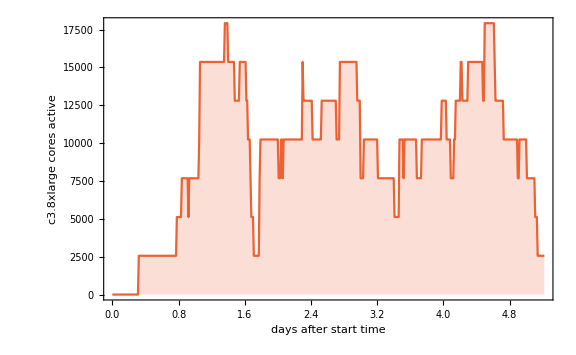

```mathematica
alignPlot=ListPlot[Transpose[{dateRange,(alignPiece/.x->#)&/@dateRange}], Joined->True, Filling->Axis, BaseStyle->{FontName->"Helvetica", FontSize->15},Frame->True, ImageSize->Large, ImagePadding->imagePadding,PlotStyle->ColorData[97,"ColorList"][[4]],FrameLabel->{{"c3.8xlarge cores active", ""}, {"days after start time","b) number of active processing cores during alignment"}}]
```

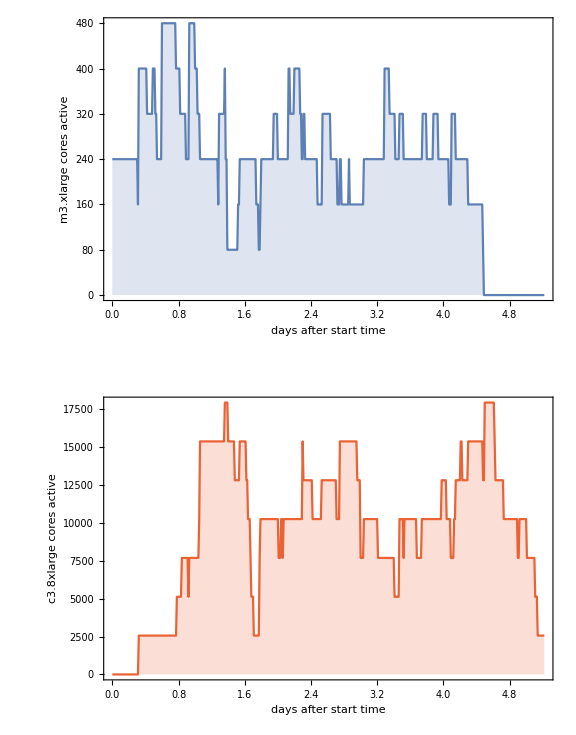

```mathematica
corePlot=GraphicsGrid[{{prepPlot},{alignPlot}}, ImageSize->Large]
```

```mathematica
Export["cores.pdf",corePlot]
```

cores.pdf